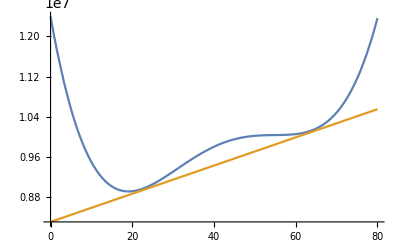

```mathematica
f[x_] := (x-3 -45)^4 + (x+7-45)^4 - 2000(x - 5-45)^2 + 10^7;
f2[x_] := 2.8*10^4 x + 8.31*10^6;
Plot[{f[x],f2[x]}, {x, 0, 80}, Ticks->None]
```

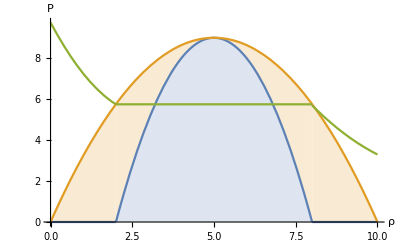

```mathematica
Plot[{(-(x-5)^2 + 9)*HeavisideTheta[x - 2]*HeavisideTheta[8 - x], -0.36(x-5)^2 + 9, (0.5(x-3)^2 + 5.25)*HeavisideTheta[2 -x] + 5.75 * HeavisideTheta[x - 2]*HeavisideTheta[8-x] + (0.2(x - 12)^2 + 2.5)*HeavisideTheta[x - 8]}, {x, 0, 10}, Filling->{1->Axis, 2-> {1}, 3-> None}, Ticks->None, AxesLabel->{"ρ","P"}]
```

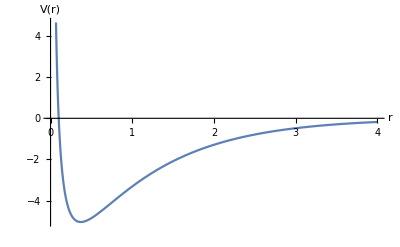

```mathematica
Plot[(1/x - 10)*Exp[-x], {x, 0, 4}, Ticks->None, AxesLabel->{"r", "V(r)"} ]
```

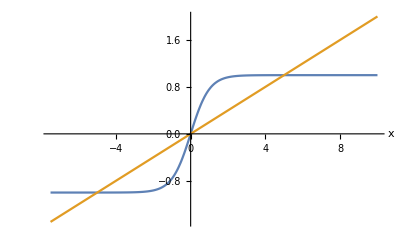

```mathematica
Plot[{Tanh[x], 0.2x}, {x, -7.5, 10}, Ticks->None, AxesLabel->{"x", None}]
```

```mathematica
GridGraph[{5, 5}]
```

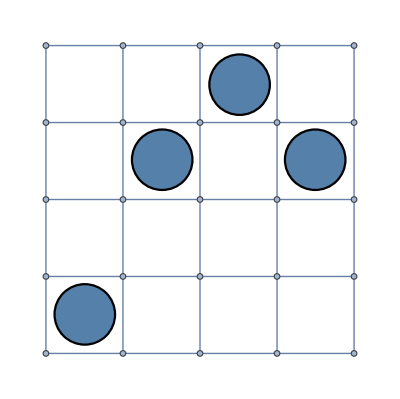

Set::write: Tag Inherited in Inherited[State] is Protected.

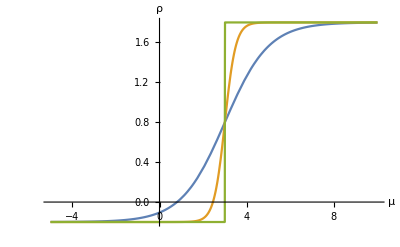

```mathematica
Plot[{Tanh[0.5x - 3*0.5] + 0.8,Tanh[2(x - 3)] + 0.8, Tanh[1000(x - 3)] + 0.8}, {x, -5, 10}, Ticks->None, AxesLabel->{"μ", "ρ"}]
```

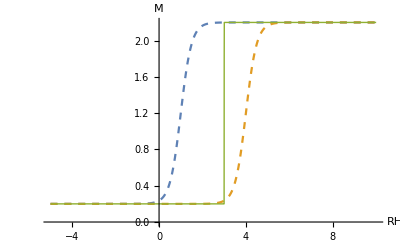

```mathematica
Plot[{Tanh[2x - 1*2] + 1.2,Tanh[2(x - 4)] + 1.2, Tanh[1000(x - 3)] + 1.2}, {x, -5, 10}, Ticks->None, AxesLabel->{"RH", "M"}, PlotStyle->{Dashed, Dashed,Thick}]
```

```mathematica
Plot[-3 + 2x, {x, 0, 5}, Ticks->None, AxesLabel->{"H", "ΔΩ"}]
```

```mathematica
Plot[((1/x)/Sinh[1/x])^2, {x, 0, 2}, Ticks->None, AxesLabel->{"T", "C"}]
```